# Complex Variables Toolkit - Final Project - Nathan Yee

## This notebook serves as a group of utilities (functions) that allow a user to interact with and understand complex functions

### The line below tells Mathematica to save all initialization cells to a .m file. This is the file that will be imported in the future whenever one wants to use the toolkit.

```mathematica
SetOptions[EvaluationNotebook[],AutoGeneratedPackage->Automatic]
```

## Point creation functions

### A large potion of this toolkit are functions that allow the user to generate massive amount of points. In particular, these points will take the shape of either circles, lines, or grids.

## Circle Creation

```mathematica
makeCirclePoints[smallRadius_,largeRadius_,numCircles_,ptsPerCircle_]:=Module[{ang, lists, pts},
ang=Range[0 Pi,2 Pi,(2π-0)/(ptsPerCircle-1)];
lists=Table[{r Cos[ang],r Sin[ang]},{r,Range[smallRadius,largeRadius,(largeRadius-smallRadius)/(numCircles-1)]}];
pts=Transpose[#]&/@lists;
Return[pts]
]
makeCirclePoints::usage="makeCirclePoints[smallRadius_,largeRadius_,numCircles_,ptsPerCircle_] makeCirclePoints returns expanding circles given smallest radius, largest radius, step size, and number of points per circle. The constant step size dictates that the radius of the circles increases by a constant step size per circle";
```

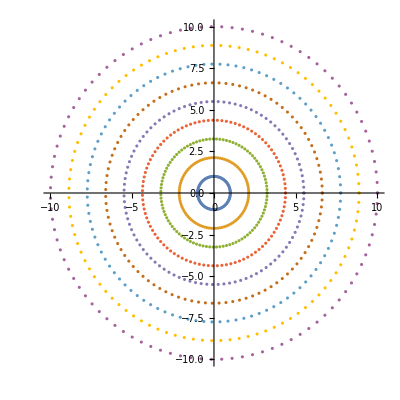

```mathematica
ListPlot[makeCirclePoints[1,10,9,100],AspectRatio->1]
```

```mathematica
makeExponentialSpacedCirclePoints[smallRadius_,largeRadius_,numCircles_,ptsPerCircle_]:=Module[{ang, lists, pts},
ang=Range[0 Pi,2 Pi,(2π-0)/(ptsPerCircle-1)];
lists=Table[{r Cos[ang],r Sin[ang]},{r,fSpace[smallRadius,largeRadius,numCircles]}];
pts=Transpose[#]&/@lists;
Return[pts]
]
makeExponentialSpacedCirclePoints::usage="makeExponentialSpacedCirclePoints[smallRadius_,largeRadius_,numCircles_,ptsPerCircle_] makeExponentialSpacedCirclePoints returns expanding circles given smallest radius, largest radius, number of circles, and number of points per circle. The number of circles dictates that the circles be spaced exponentially within the largestRadius - smallestRadius range";
```

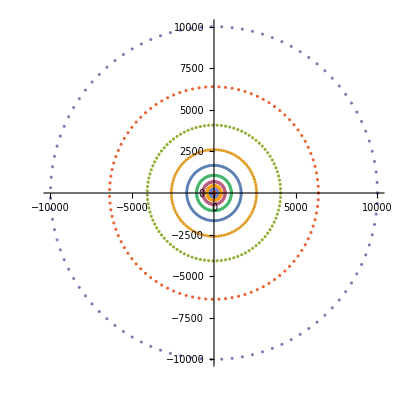

```mathematica
ListPlot[makeExponentialSpacedCirclePoints[2,10000,20,100],AspectRatio->1,PlotRange->Full]
```

```mathematica
makeSphereSpacedCirclePoints[numCircles_,ptsPerCircle_]:=Module[{ang, lists, pts},
ang=Range[0 Pi,2 Pi,(2π-0)/(ptsPerCircle-1)];
lists=Table[{r Cos[ang],r Sin[ang]},{r,makeSphereSpacedPoints[numCircles]}];
pts=Transpose[#]&/@lists;
Return[pts]
]
makeSphereSpacedCirclePoints::usage="makeSphereSpacedCirclePoints[numCircles_,ptsPerCircle_] makeSphereSpacedCirclePoints returns circles based on inverse stereographic projection given a number of circles, and the number of points per circle";
```

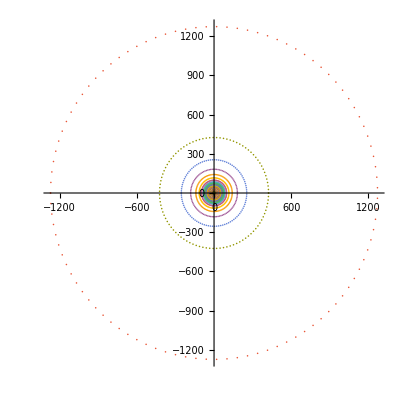

```mathematica
ListPlot[makeSphereSpacedCirclePoints[1000,100],AspectRatio->1,PlotRange->Full]
```

## Various Spacings

### Inverse (default Log) spaced points

```mathematica
fSpace[min_,max_,numPts_,f_: Log]:=Module[{},N[InverseFunction[f]/@Range[f@min,f@max,(f@max-f@min)/(numPts-1)]]]
fSpace::usage="fSpace[min, max, steps, Log] gives inverse f (default Log) spaced points from min to max over a given number of points";
```

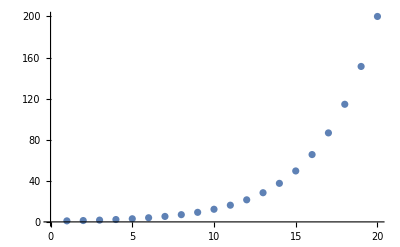

```mathematica
ListPlot[fSpace[1,200,20,Log]]
```

### Sphere spaced points

```mathematica
makeRiemannRealAxis[numPts_]:=Module[
{angles, pts},
angles=N@Range[0Pi,2Pi,(2 Pi - 0Pi)/(numPts - 1)];
pts=Table[{Cos[ang],0,Sin[ang]},{ang,angles}];
Return[pts]
]
makeRiemannRealAxis::usage="makeRiemannRealAxis[numPts_] makeRiemannRealAxis returns equally spaced points around the positive real axis on the Riemann Sphere";
```

```mathematica
realAxis3D=makeRiemannRealAxis[30];
ListPointPlot3D[realAxis3D,AspectRatio->1,PlotStyle->PointSize[.03],ImageSize->Large]
```

-Graphics3D-

```mathematica
riemannPointToComplexPlane[{X_,Y_,Z_}]:=Module[{sol,pair},
sol=Solve[{x+ⅈ y==(X+ⅈ Y)/(1-Z)},{x∈Reals,y∈Reals}];
pair=({x,y}/.sol)[[1]];
Return[pair]
]
riemannPointToComplexPlane::usage="riemannPointToComplexPlane[{X_,Y_,Z_}] riemannPointToComplexPlane returns the inverse stereographic projection of a point distance 1 from the origin in 3D space";
```

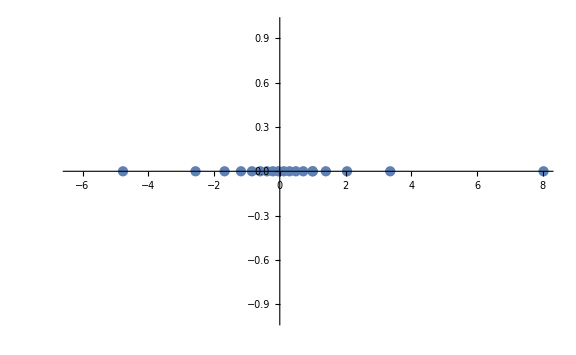

```mathematica
realAxis2D=riemannPointToComplexPlane[#]&/@realAxis;
ListPlot[realAxis2D,ImageSize->Large]
```

```mathematica
makeSphereSpacedPoints[numPts_]:=Module[{pts,complexPts,realPts},
pts=makeRiemannRealAxis[numPts];
complexPts=riemannPointToComplexPlane[#]&/@pts;
realPts=complexPts[[All,1]];
Return[realPts]
]
makeSphereSpacedPoints::usage="makeSphereSpacedPoints[numPts_] makeSphereSpacedPoints returns the inverse stereographic projection of points around the positive real axis on the Riemann Sphere. It gets the positive real axis of the Riemann Sphere by calling makeRiemannRealAxis. It finds the inverse stereographic projection of the points by mapping riemannPointToComplexPlane onto each point";
```

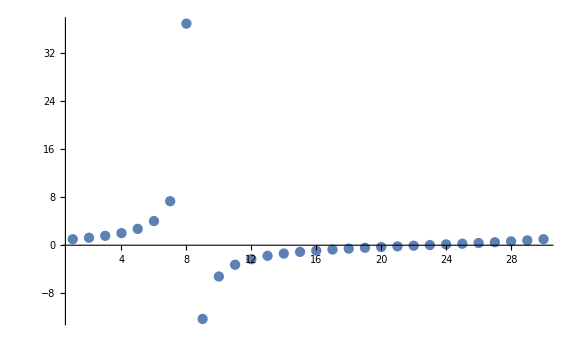

```mathematica
ListPlot[makeSphereSpacedPoints[30],PlotRange->All,ImageSize->Large]
```

## Complex Plane to Image Plane

### plotImage takes in a list of points, a complex function, and two plot ranges and outputs the original and its image.

```mathematica
getImagePts[expr_,pts_]:=Module[{imgPts},
imgPts={Re[expr /. z -> #[[1]] + ⅈ #[[2]]], Im[expr /. z -> #[[1]] + ⅈ #[[2]]]}&/@#&/@pts;
Return[imgPts]]
getImagePts::usage="getImagePts[expr[z],pts] returns the image points given takes in an expression of z and a list of lists of lists of points";
```

```mathematica
getImagePts[z+1-ⅈ,{{{1,1},{2,2}}}]
```

{{{2,0},{3,1}}}

```mathematica
plotImage[pts_,expr_,pltRange1_:Automatic,PltRange2_:Automatic,colors_:1]:=Module[{},
If[colors==1,colors=RGBColor[1,1,1],colors=colors];
{
Graphics[MapThread[{#1, Thick, Line[#2]}&,{colors,pts}], PlotRange -> pltRange1, Axes -> True, Background -> White, ImageSize -> {300,300}, AxesLabel -> {Style["x",Italic], Style["y",Italic]},ImagePadding->20],

Graphics[MapThread[{#1, Thick, Line[{Re[expr /. z -> #[[1]] + ⅈ #[[2]]], Im[expr /. z -> #[[1]] + ⅈ #[[2]]]}& /@ #2]}&,{colors,pts}], PlotRange -> PltRange2, Axes -> True, Background -> White, ImageSize -> {300,300}, AxesLabel -> {Style["u",Italic], Style["v",Italic]},ImagePadding->20]
}
]
plotImage::usage="plotImage[pts,expr,pltRange1:Automatic,PltRange2:Automatic,colors:1] returns a list containing the complex and image plots given a list of lists of lists of points, an expression of z, two plot ranges (can be Automatic), and a list of colors";
```

{RGBColor[0.5, 0.1, 0.7],RGBColor[0.5, 0.3666666666666667, 0.7],RGBColor[0.5, 0.6333333333333333, 0.7],RGBColor[0.5, 0.9, 0.7]}

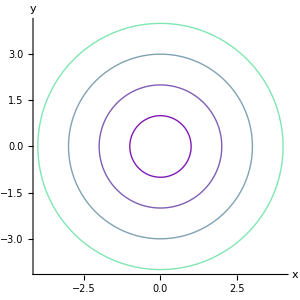
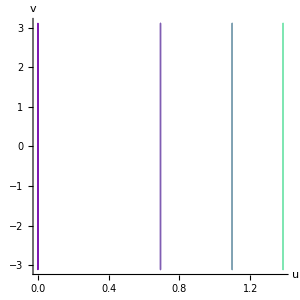
Complex Plane | ImagePlane
-Graphics- | -Graphics-

```mathematica
circles=Quiet[makeCirclePoints[1,4,4,100]];
circleColors=makeColorGradient[circles]
Quiet@Grid[{{"Complex Plane","ImagePlane"},plotImage[circles,Log[z],Automatic,Automatic,circleColors]}]//TraditionalForm
```

### makeGridPoints will make a grid of lines given user entered parameters

```mathematica
makeVerticalPts[min_,max_,ptsPerLine_,numLines_]:=Module[{horiPts},
horiPts=Table[Table[{x,y},{y,Range[min,max,(max-min)/(ptsPerLine-1)]}],{x,min,max,(max-min)/(numLines-1)}];
Return[horiPts]
]

makeHorizontalPts[min_,max_,ptsPerLine_,numLines_]:=Module[{horiPts},
horiPts=Table[Table[{x,y},{x,Range[min,max,(max-min)/(ptsPerLine-1)]}],{y,min,max,(max-min)/(numLines-1)}];
Return[horiPts]
]

makeGridPts[min_,max_,ptsPerLine_,numLines_]:=Module[{vertPts,horiPts,pts},
vertPts=makeVerticalPts[min,max,ptsPerLine,numLines];
horiPts=makeHorizontalPts[min,max,ptsPerLine,numLines];
pts=Join[horiPts,vertPts];
Return[pts]
]
```

```mathematica
makeLogVerticalPts2[min_,max_,ptsPerLine_,numLines_]:=Module[{vertPts},
vertPts=Table[Table[{x,y},{y,fSpace[min,max,ptsPerLine]}],{x,min,max,(max-min)/(numLines-1)}];
Return[Re[vertPts]]
]

makeLogHorizontalPts2[min_,max_,ptsPerLine_,numLines_]:=Module[{horiPts},
horiPts=Table[Table[{x,y},{x,fSpace[min,max,ptsPerLine]}],{y,min,max,(max-min)/(numLines-1)}];
Return[Re[horiPts]]
]

makeLogGridPts[min_,max_,ptsPerLine_,numLines_]:=Module[{vertLogPts,horiLogPts,pts},
vertLogPts=makeLogVerticalPts[min,max,ptsPerLine,numLines];
horiLogPts=makeLogHorizontalPts[min,max,ptsPerLine,numLines];
pts=Join[horiLogPts,vertLogPts];
Return[pts]
]
```

```mathematica
makeLogVerticalPts[min_,max_,ptsPerLine_,numLines_]:=Module[{posVertPts,negVertPts,pts},
posVertPts=Table[Table[{x,y},{y,fSpace[.001,max,Floor[ptsPerLine/2]]}],{x,min,max,(max-min)/(numLines-1)}];
negVertPts=Table[Table[{x,y},{y,fSpace[min,-.001,Floor[ptsPerLine/2]]}],{x,min,max,(max-min)/(numLines-1)}];
pts=MapThread[Join,{negVertPts,posVertPts}];
Return[Re[pts]]
]

makeLogHorizontalPts[min_,max_,ptsPerLine_,numLines_]:=Module[{posHoriPts,negHoriPts,pts},
posHoriPts=Table[Table[{x,y},{x,fSpace[.01,max,Floor[ptsPerLine/2]]}],{y,min,max,(max-min)/(numLines-1)}];
negHoriPts=Table[Table[{x,y},{x,fSpace[min,-.01,Floor[ptsPerLine/2]]}],{y,min,max,(max-min)/(numLines-1)}];
pts=MapThread[Join,{negHoriPts,posHoriPts}];
Return[Re[pts]]
]
```

```mathematica
makeRandomColors[pts_]:=Module[{colors},
colors=RandomColor[Length[pts]];
Return[colors]]

makeColorGradient[pts_]:=Module[{colors},
colors=Table[RGBColor[.5,x,.7],{x,.1,.9,(.9-.1)/(Length[pts]-1)}];
Return[colors]]
```

### Equal space test constants

```mathematica
numPts=1000;
numLines=3;
min=-10;
max=10;
expr=z^3
```

z^3

#### first make vertical lines

{7,1,2}

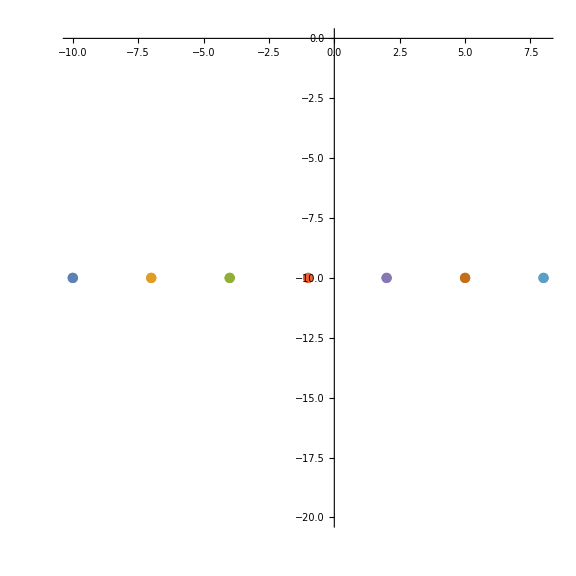

```mathematica
vertPts=makeVerticalPts[min,max,numPts,numLines];
Dimensions[vertPts]
ListPlot[vertPts,ImageSize->Large,AspectRatio->1]
```

#### second horizontal lines

{7,1,2}

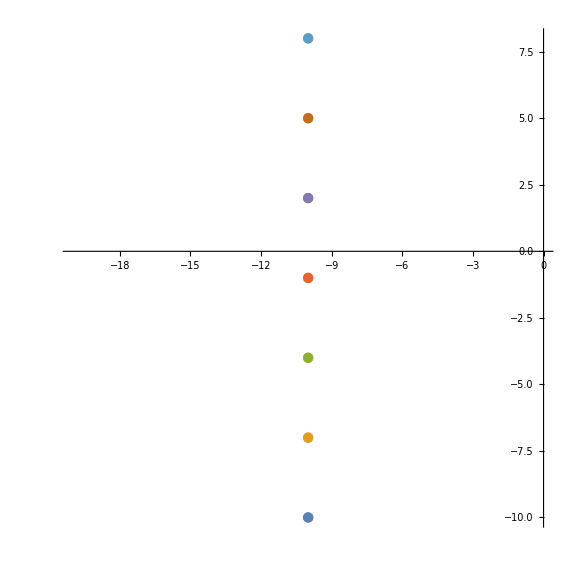

```mathematica
horiPts=makeHorizontalPts[min,max,numPts,numLines];
Dimensions[horiPts]
ListPlot[horiPts,ImageSize->Large,AspectRatio->1]
```

### Log test constants

```mathematica
ptsPerLine=100;
numLines=3;
min=-100;
max=100;
expr=z^3
```

z^3

{3,100,2}

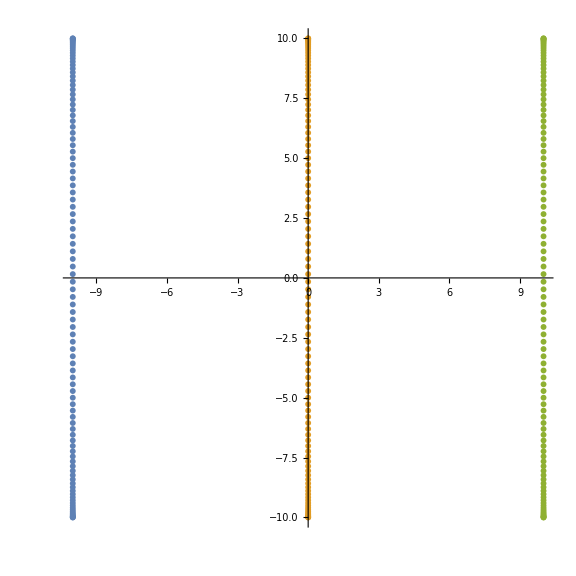

```mathematica
logVertPts=makeLogVerticalPts2[-10,10,ptsPerLine,numLines];
Dimensions[logVertPts]
ListPlot[logVertPts,ImageSize->Large,AspectRatio->1]
```

```mathematica
Range[-10,10,20/(21-1)]
```

{-10,-9,-8,-7,-6,-5,-4,-3,-2,-1,0,1,2,3,4,5,6,7,8,9,10}

```mathematica
Log[0]
```

-∞

```mathematica
N@Re@Log[Range[-3,3,1/10]]
```

{1.09861,1.06471,1.02962,0.993252,0.955511,0.916291,0.875469,0.832909,0.788457,0.741937,0.693147,0.641854,0.587787,0.530628,0.470004,0.405465,0.336472,0.262364,0.182322,0.0953102,0.,-0.105361,-0.223144,-0.356675,-0.510826,-0.693147,-0.916291,-1.20397,-1.60944,-2.30259,-∞,-2.30259,-1.60944,-1.20397,-0.916291,-0.693147,-0.510826,-0.356675,-0.223144,-0.105361,0.,0.0953102,0.182322,0.262364,0.336472,0.405465,0.470004,0.530628,0.587787,0.641854,0.693147,0.741937,0.788457,0.832909,0.875469,0.916291,0.955511,0.993252,1.02962,1.06471,1.09861}

#### first make vertical lines

{3,100,2}

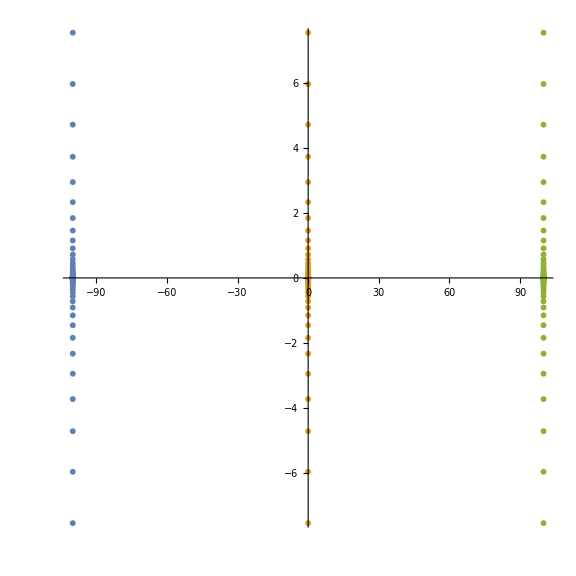

```mathematica
logVertPts=makeLogVerticalPts[min,max,ptsPerLine,numLines];
Dimensions[logVertPts]
ListPlot[logVertPts,ImageSize->Large,AspectRatio->1]
```

#### second horizontal lines

{3,100,2}

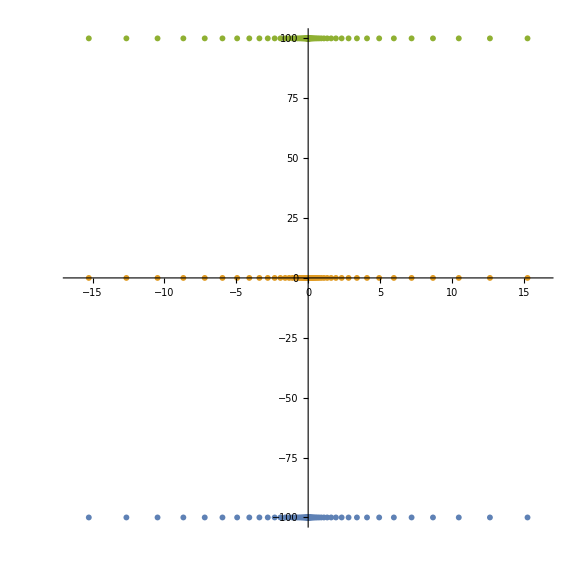

```mathematica
logHoriPts=makeLogHorizontalPts[min,max,ptsPerLine,numLines];
Dimensions[logHoriPts]
ListPlot[logHoriPts,ImageSize->Large,AspectRatio->1]
```

### Next try to make a grid

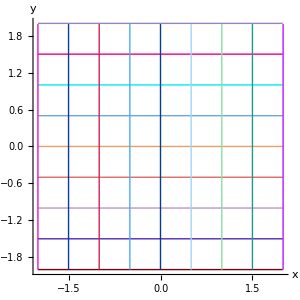
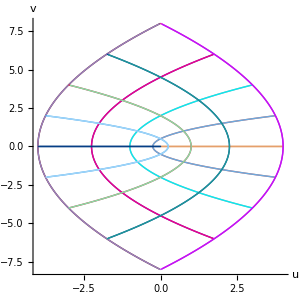

```mathematica
gridPts=makeGridPts[-2,2,.005,.5];
gridColors=makeRandomColors[gridPts];
plotImage[gridPts,z^2,Automatic,10,gridColors]
```

## Experiment with Riemann sphere stereographic projection

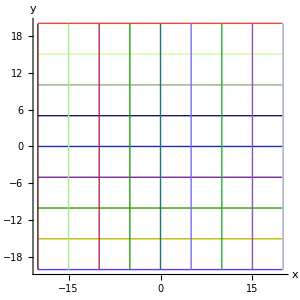
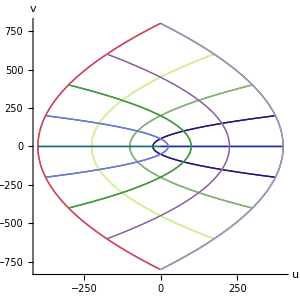

```mathematica
gridPts=makeGridPts[-20,20,.1,5];
gridColors=makeRandomColors[gridPts];
plotImage[gridPts,z^2,Automatic,10,gridColors]
```

```mathematica
gridPts[[1]][[1]]
```

{-20.,-20}

```mathematica
complexTo3D[point_]:=Module[{x,y,z,mix,X,Y,Z},
x=point[[1]];
y=point[[2]];
mix=(2x+ⅈ 2y)/(1+x^2+y^2);
X=Re[mix];
Y=Im[mix];
z=x+ⅈ y;
Z=(Abs[z]^2-1)/(Abs[z]^2+1);
Return[{X,Y,Z}]
]

complexPtsTo3D[points_]:=Module[{spherePts3D},
spherePts3D=complexTo3D[#]&/@#&/@points;
Return[spherePts3D]
]
```

```mathematica
complexTo3D[{1,1}]
```

{2/3,2/3,1/3}

```mathematica
pts3D=complexTo3D[#]&/@#&/@gridPts;
colors3D=makeRandomColors[pts3D]
```

{RGBColor[0.21957988552975127, 0.16982268801903966, 0.07201540725177535],RGBColor[0.6349407100697082, 0.5688675163639412, 0.28938401896489685],RGBColor[0.937455906402628, 0.7442995066407192, 0.423111887738592],RGBColor[0.9497954748135078, 0.9726832786169239, 0.6301929149987868],RGBColor[0.8072976056403744, 0.5829090854787489, 0.09458548200884231],RGBColor[0.6813094194231937, 0.019577966742676978, 0.5424640080357646],RGBColor[0.04848229557935979, 0.8148878787869487, 0.5475376055738272],RGBColor[0.05048568542732346, 0.5516132570787782, 0.6643889990323406],RGBColor[0.9118896326779038, 0.24073695800559358, 0.705009336514197],RGBColor[0.34940471420686925, 0.2596988824860649, 0.5463470800300259],RGBColor[0.6652058584714331, 0.5981125077125959, 0.9228010015761672],RGBColor[0.8335544809017181, 0.3463073931367149, 0.1298768054749786],RGBColor[0.8757104297255178, 0.7721026412150171, 0.8467494898697863],RGBColor[0.6618131974270363, 0.5908929886853942, 0.3482948402294046],RGBColor[0.9234458952268318, 0.7940604710779882, 0.0023713335403170444],RGBColor[0.07770528840194024, 0.9311698763834175, 0.9030312957656543],RGBColor[0.8573439847571895, 0.4524105115531971, 0.2278862435603488],RGBColor[0.3161819006654252, 0.7096094974002662, 0.42888462383976367]}

```mathematica
ListPointPlot3D[pts3D,PlotRange->All,AspectRatio->1,ImageSize->Large]
```

-Graphics3D-

```mathematica
Graphics3D[MapThread[{#1,Thick,Line[#2]}&,{colors3D,pts3D}]]
```

-Graphics3D-

### 1 to 100 log spaced

```mathematica
Re@fSpace[-20,20,100]
```

{-20.,-19.9899,-19.9597,-19.9094,-19.8391,-19.7488,-19.6386,-19.5086,-19.359,-19.1899,-19.0014,-18.7939,-18.5674,-18.3222,-18.0585,-17.7767,-17.477,-17.1597,-16.8251,-16.4735,-16.1054,-15.7211,-15.3209,-14.9053,-14.4747,-14.0295,-13.5702,-13.0972,-12.6111,-12.1122,-11.6011,-11.0784,-10.5445,-10.,-9.44542,-8.88133,-8.3083,-7.7269,-7.13772,-6.54136,-5.93841,-5.32948,-4.71518,-4.09613,-3.47296,-2.8463,-2.21676,-1.585,-0.951638,-0.317319,0.317319,0.951638,1.585,2.21676,2.8463,3.47296,4.09613,4.71518,5.32948,5.93841,6.54136,7.13772,7.7269,8.3083,8.88133,9.44542,10.,10.5445,11.0784,11.6011,12.1122,12.6111,13.0972,13.5702,14.0295,14.4747,14.9053,15.3209,15.7211,16.1054,16.4735,16.8251,17.1597,17.477,17.7767,18.0585,18.3222,18.5674,18.7939,19.0014,19.1899,19.359,19.5086,19.6386,19.7488,19.8391,19.9094,19.9597,19.9899,20.}

```mathematica
Range[-1,1,(1-(-1))/(20-1)]
```

{-1,-17/19,-15/19,-13/19,-11/19,-9/19,-7/19,-5/19,-3/19,-1/19,1/19,3/19,5/19,7/19,9/19,11/19,13/19,15/19,17/19,1}

## Log grid Riemann sphere

```mathematica
ptsPerLine=100;
numLines=5;
min=-10000;
max=10000;
expr=z^3
```

z^3

```mathematica
logGridPts=makeLogGridPts[min,max,ptsPerLine,numLines];
Dimensions[logGridPts]
```

{10,100,2}

```mathematica
logPts3D=pts3D=complexTo3D[#]&/@#&/@logGridPts;
Dimensions[logPts3D]
```

{10,100,3}

```mathematica
colors3D=makeRandomColors[logPts3D]
```

{RGBColor[0.49711261580179045, 0.563701962949382, 0.21069430978679993],RGBColor[0.08895948718146673, 0.5844437988646287, 0.7519435749398089],RGBColor[0.6279276405198018, 0.9798261518454896, 0.7636201033664458],RGBColor[0.9312209093293893, 0.11693809314275416, 0.20893112959080495],RGBColor[0.8887307640436688, 0.23488927442110108, 0.5185012224272301],RGBColor[0.6952978796786331, 0.8294596668304697, 0.7714847270919509],RGBColor[0.7775086496562584, 0.3463391961572355, 0.04861520792934804],RGBColor[0.01970077375194279, 0.2911436655991295, 0.6563305305163136],RGBColor[0.3465965837020848, 0.3964463510781837, 0.12641764080732187],RGBColor[0.7438810865103698, 0.6431150618987245, 0.024946124501054046]}

```mathematica
ListPointPlot3D[logPts3D,PlotRange->All,AspectRatio->1,ImageSize->Large]
```

-Graphics3D-

```mathematica
Graphics3D[MapThread[{#1,Thick,Line[#2]}&,{colors3D,pts3D}]]
```

-Graphics3D-

## Trying to get circular spaced points

```mathematica
makeHorizontalLines[min_,max_,ptsPerLine_,numLines_]:=Module[{horiPts,spherePts},
spherePts=makeSphereSpacedPoints[ptsPerLine];
horiPts=Table[Table[{x,y},{x,spherePts}],{y,min,max,(max-min)/(numLines-1)}];
Return[horiPts]
]
makeVerticalLines[min_,max_,ptsPerLine_,numLines_]:=Module[{horiPts,spherePts},
spherePts=makeSphereSpacedPoints[ptsPerLine];
horiPts=Table[Table[{x,y},{y,spherePts}],{x,min,max,(max-min)/(numLines-1)}];
Return[horiPts]
]
makeGrid[min_,max_,ptsPerLine_,numLines_]:=Module[{vertPts,horiPts,pts},
vertPts=makeHorizontalLines[min,max,ptsPerLine,numLines];
horiPts=makeVerticalLines[min,max,ptsPerLine,numLines];
pts=Join[horiPts,vertPts];
Return[pts]
]
makeGrid::usage="makeGrid[min,max,ptsPerLine,numLines] makes a grid of sphere spaced points given line bounds of min, max, ptsPerLine, and numLines"
```

makeGrid[min,max,ptsPerLine,numLines] makes a grid of sphere spaced points given line bounds of min, max, ptsPerLine, and numLines

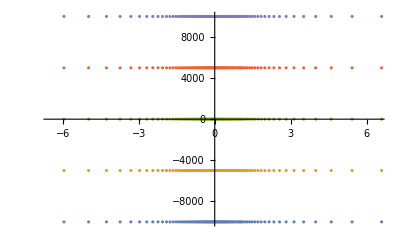

```mathematica
horiPts=makeHorizontalLines[min,max,ptsPerLine,numLines];
ListPlot[horiPts]
```

```mathematica
horiPts//Dimensions
```

{5,100,2}

```mathematica
expr=1/z;
image={Re[expr /. z -> #[[1]] + ⅈ #[[2]]], Im[expr /. z -> #[[1]] + ⅈ #[[2]]]}&/@#&/@horiPts;
Dimensions[image]
```

{5,100,2}

```mathematica
min=-3;
max=3;
ptsPerLine=200;
numLines=3;
```

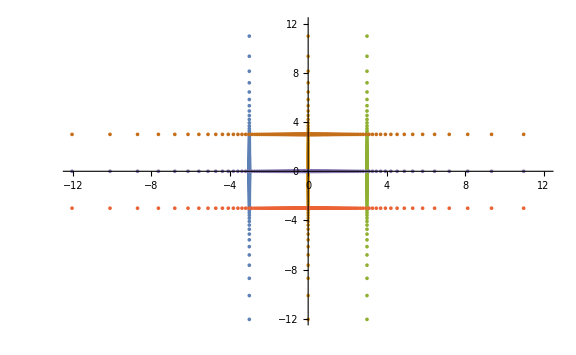

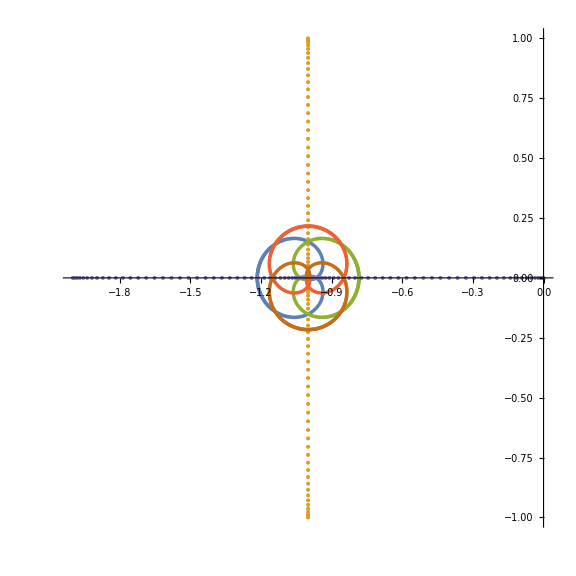

```mathematica
expr=(z^3-1);
gridPts=makeGrid[min,max,ptsPerLine,numLines];
ListPlot[gridPts]
spherePts3D=complexTo3D[#]&/@#&/@gridPts;
image=getImagePts[expr,spherePts3D];
ListPlot[image,PlotRange->Full,ImageSize->Large,AspectRatio->1]
```

## 3D printing

```mathematica
Graphics3D[Join[cylinders[complexPtsTo3D[image],.03],{Opacity[.3],Sphere[{0,0,0}]}]];
```

```mathematica
tubes[pts_,radius_]:=Module[{},Tube[#,radius]&/@complexPtsTo3D[pts]]
```

```mathematica
Graphics3D[tubes[gridPts,.05]];
```

```mathematica
takingPts[takes_,pts_]:=Module[{newPts},
newPts=Take[pts,#]&/@takes;
Return[newPts]]

cylinderPts[pts_]:=Module[{takes,returnPts},
takes=Table[{x,x+1},{x,1,Dimensions[pts][[2]]-1}];
returnPts=takingPts[takes,#]&/@pts
]

cylinders[pts_,radius_]:=Module[{},
Return[Cylinder[#,radius]&/@#&/@cylinderPts[pts]]]
```

```mathematica
Graphics3D[tubes[gridPts,.05]]
```

-Graphics3D-

```mathematica
Export["grid2.stl",Graphics3D[tubes[gridPts,.05]],{"STL,","BinaryFormat"->True}]
```

grid2.stl

```mathematica
Import["grid2.stl"]
```

-Graphics3D-

```mathematica
Graphics3D[cylinders[complexPtsTo3D[makeGrid[-1,1,100,12]],.01]]
```

-Graphics3D-

```mathematica
Export["grid_10_7.stl",Graphics3D[cylinders[complexPtsTo3D[makeGrid[-1,1,100,12]],.01]],{"STL,","BinaryFormat"->True}]
```

grid_10_7.stl

```mathematica
grid107=Import["grid_10_7.stl"]
```

-Graphics3D-

## Newtons method

```mathematica
makeNewtonMethodAnimation[plotRange_,map_,depth_,points_]:=Module[{localPts},
localPts=points;
plots=Flatten[{
{ListPlot[localPts,PlotRange->{{-plotRange,plotRange}, {-plotRange,plotRange}},PlotStyle->PointSize[.02],AspectRatio->1,ImageSize->Large]},
Table[
(*Apply map to grid pts*) localPts=getImagePts[map,localPts];
ListPlot[localPts,PlotRange->{{-plotRange,plotRange}, {-plotRange,plotRange}},PlotStyle->PointSize[.02],AspectRatio->1,ImageSize->Large]
,{n,1,depth}]
}];
Return[Manipulate[plots[[n]],{n,1,Length[plots],1}]]]
makeNewtonMethodAnimation::usage="makeNewtonMethodAnimation[plotRange,map,depth,points] makes animation of successive mappings";
```

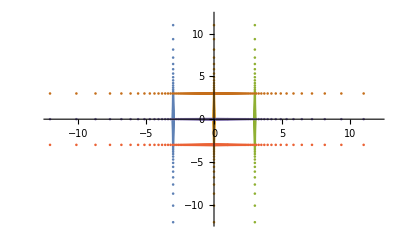

```mathematica
expr=(z-z/3+1/(3 z^2));
gridPts=makeGrid[min,max,ptsPerLine,numLines];
ListPlot[gridPts]
```